```mathematica
Remove["Global`*"];
ClearAll[simulatePopulations]
simulatePopulations[initialDoves_, initialHawks_, numLists_, numIterations_, printing_: 0] := Module[
    {doves = initialDoves, hawks = initialHawks, lists, processInteractions, 
     addToList, initializeLists, printTable = {{"Iteration", "Doves", "Hawks", 
        "Ratio of Doves", "One Dove", "One Hawk", "Two Doves", "Two Hawks", "D&H"},{0,initialDoves,initialHawks,N[initialDoves/(initialDoves+initialHawks)],0,0,0,0,0}}, 
     oneDove, oneHawk, twoDoves, twoHawks, doveAndHawk},
    
    initializeLists[count_] := Table[{}, {count}];
    
    addToList[listOfLists_, element_] := Module[
        {availableLists, randomIndex, updatedList = listOfLists},
        availableLists = Select[Range[Length[updatedList]], Length[updatedList[[#]]] < 2 &];
        If[Length[availableLists] > 0,
            randomIndex = RandomChoice[availableLists];
            updatedList[[randomIndex]] = Append[updatedList[[randomIndex]], element];
            updatedList,
            Print["All lists are full."];
            listOfLists
        ]
    ];
    
    processInteractions[pairs_] := Module[{newDoves = 0, newHawks = 0, u=RandomReal[]},
        Do[
            Switch[pair,
                {1}, newDoves += 2; oneDove++,
                {2}, newHawks += 2; oneHawk++,
                {1, 1}, newDoves += 2; twoDoves++,
                (*{2, 2}, Which[u<0.25, newHawks++,u<0.5, newHawks+=2]; twoHawks++,*)
      {2, 2},If[RandomReal[]>0.25,newHawks++];If[RandomReal[]>0.25,newHawks++]; twoHawks++,
                {1, 2} | {2, 1},
                If[RandomReal[] < 0.5, newHawks += 1, newHawks += 2];
                If[RandomReal[] < 0.5, newDoves += 0, newDoves += 1];
                doveAndHawk++
            ],
            {pair, pairs}
        ];
        {newDoves, newHawks}
    ];
    
    appendToTable[iter_, doves_, hawks_] := Module[{total = doves + hawks, ratio},
        ratio = If[total > 0, N[doves/total], 0];
        AppendTo[printTable, {iter, doves, hawks, ratio, oneDove, oneHawk, twoDoves, twoHawks, doveAndHawk}]
    ];
    
    lists = initializeLists[numLists];
    
    For[i = 1, i ≤ numIterations && (doves > 0 || hawks > 0), i++,
        oneDove = 0; oneHawk = 0; twoDoves = 0; twoHawks = 0; doveAndHawk = 0;
        While[doves > 0 || hawks > 0,
            If[Length@Position[lists, l_List /; Length[l] < 2] == 0,
                (*Print[lists];*)
                (*Print["Failed to add elements: All lists are full."];*)
                Break[]
            ];
            rand = RandomChoice[{doves, hawks} -> {1, 2}];
            If[rand == 1,
                lists = addToList[lists, 1];
                doves--,
                lists = addToList[lists, 2];
                hawks--
            ]
        ];
        {doves, hawks} = processInteractions[lists];
        appendToTable[i, doves, hawks];
        lists = initializeLists[numLists]
    ];
    
    If[printing == 1,
        Print[Grid[printTable, Frame -> All, Alignment -> Center, 
          Background -> {None, {LightBlue, None}}]]
    ];
    
    {printTable}
]
```

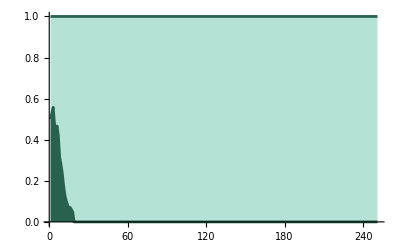

```mathematica
color1=RGBColor@@HexColorToRGB["#b4e2d4"];
color2=RGBColor@@HexColorToRGB["#f4ce14"];
outlineColor=RGBColor@@HexColorToRGB["#28624e"];
expectedColor=RGBColor@@HexColorToRGB["#1e3931"];
lineColor=RGBColor@@HexColorToRGB["#000000"];
thickness=0.005;
i=250;
p1=Plot[1,{x,1,i+1},Filling->Bottom,FillingStyle->color1,PlotStyle->outlineColor,AxesStyle->Directive[expectedColor,Thickness[thickness]]];
p2=ListPlot[simulatePopulations[10,10,100,i,0][[1]][[2;;-1,4]],Joined->True,Filling->Bottom,FillingStyle->outlineColor,PlotRange->{0,1},PlotStyle->outlineColor,AxesStyle->Directive[outlineColor,Thickness[thickness]]];
p3=Plot[0.5,{x,1,i+1},PlotStyle->lineColor,AxesStyle->Directive[expectedColor,Thickness[thickness]]];
plot=Show[p1,p2,PlotRange->{0,1}]
```

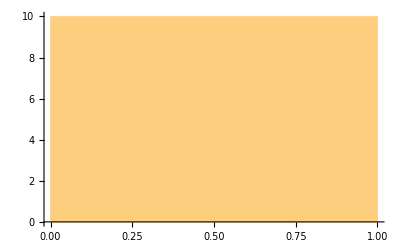

Xbar:0.

sX:0.

95% CI : {0.,0.}

Max error : 0.

```mathematica
n=10;
data := Last[simulatePopulations[10, 10, 100, 150, 0][[1]][[2;;-1, 4]]]
dataTable=Table[data,{n}];
Histogram[dataTable]
Xbar=Mean[dataTable];
sX = StandardDeviation[dataTable];
Print["Xbar:",Xbar]
Print["sX:",sX]
Print["95% CI : ",{Xbar - 1.96 sX/Sqrt[n] , Xbar + 1.96 sX/Sqrt[n]}]
Print["Max error : ",1.96 sX/Sqrt[n]]
```